# Homework 2: Detection of Vacuum Fluctuations

## 1. Physical Parameters

Let us define the constants as indicated in the text

```mathematica
a=1000^-1;
λ=10^-5;
```

### a)

We begin by computing with our analytical result (★)

```mathematica
TableForm[Table[{T,N[(T^2 λ^2)/(4π)ⅇ^(-T^2/2)1/((a^2+T^2)^(3/2))(√(a^2+T^2)-√(π/2)T^2 ⅇ^(T^4/(2(a^2+T^2)))Erfc[T^2/(√(2(a^2+T^2)))])]},{T,{0.1,1,10,100,1000}}],TableHeadings->{None,{"T(Ω^-1)","P_(g →  e)"}}]
```

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-500000.] is too small to represent as a normalized machine number; precision may be lost.

T(Ω^-1) | P_(g →  e)
0.1 | 6.99949×10^-12
1 | 1.6619×10^-12
10 | 1.49096×10^-35
100 | 0.
1000 | 0.

We now proceed to confirm these result through the numerical computation of (●)

```mathematica
TableForm[Table[{T,(T^2 λ^2)/(4π)NIntegrate[u ⅇ^(-1/2 a^2 u^2)ⅇ^(-1/2 T^2(1+u)^2),{u,0,∞}]},{T,{0.1,1,10,100,1000}}],TableHeadings->{None,{"T(Ω^-1)","P_(g →  e)"}}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

T(Ω^-1) | P_(g →  e)
0.1 | 6.99949×10^-12
1 | 1.6619×10^-12
10 | 1.49096×10^-35
100 | 0.
1000 | 0.

and (■) of the Gaussian switching function

```mathematica
TableForm[Table[{T,NIntegrate[λ^2/((2π)^3 2Norm[{kx,ky,kz}])ⅇ^(-1/2 a^2 Norm[{kx,ky,kz}]^2)Abs[FourierTransform[ⅇ^(-t^2/T^2),t,1+Norm[{kx,ky,kz}],FourierParameters->{1, -1}]]^2,{kx,-∞,∞},{ky,-∞,∞},{kz,-∞,∞}]},{T,{0.1,1,10,100,1000}}],TableHeadings-> {None,{"T(Ω^-1)","P_(g →  e)"}}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

T(Ω^-1) | P_(g →  e)
0.1 | 6.99949×10^-12
1 | 1.6619×10^-12
10 | 1.49096×10^-35
100 | 0.
1000 | 0.

### b)

The agreement of the results above gives us confidence that the probabilities for the sudden switching function are well described by the numerical computation of (◆)

```mathematica
TableForm[Table[{T,λ^2/π^2 NIntegrate[u/(1+u)^2 ⅇ^(-1/2 a^2 u^2)Sin[((1+u)T)/2]^2,{u,0,∞}]},{T,{0.1,1,10,100,1000}}],TableHeadings->{None,{"T(Ω^-1)","P_(g →  e)"}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 2.54411 and 0.0000102075 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 3.11061 and 0.0000270107 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 2.9796 and 0.0000271857 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

T(Ω^-1) | P_(g →  e)
0.1 | 2.57772×10^-11
1 | 3.1517×10^-11
10 | 3.01897×10^-11
100 | 3.02358×10^-11
1000 | 3.02353×10^-11

and (■) of this switching

```mathematica
TableForm[Table[{T,NIntegrate[λ^2/((2π)^3 2Norm[{kx,ky,kz}])ⅇ^(-1/2 a^2 Norm[{kx,ky,kz}]^2)Abs[FourierTransform[Piecewise[{{1, Abs[t]≤ T/2}, {0, Abs[t]>T/2}}],t,1+Norm[{kx,ky,kz}],FourierParameters->{1, -1}]]^2,{kx,-∞,∞},{ky,-∞,∞},{kz,-∞,∞}]},{T,{0.1,1,10,100,1000}}],TableHeadings-> {None,{"T(Ω^-1)","P_(g →  e)"}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.57772×10^-11 and 1.04682×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.15174×10^-11 and 1.83028×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.01916×10^-11 and 6.42967×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

T(Ω^-1) | P_(g →  e)
0.1 | 2.57772×10^-11
1 | 3.15174×10^-11
10 | 3.01916×10^-11
100 | 3.54192×10^-11
1000 | 3.39258×10^-11

The matching between the first three values of the last two calculations gives us confidence that the simplifications done to arrive to (◆) from (■) were correct. Since the expression is much simpler and the run time is much smaller, we will use the expression (◆) for the rest of the computations.

### d)

Now we redefine (★) and (◆) so that they depend on a instead of T.

```mathematica
Clear[a];
T=1;
```

```mathematica
TableForm[Table[{a,N[(T^2 λ^2)/(4π)ⅇ^(-T^2/2)1/((a^2+T^2)^(3/2))(√(a^2+T^2)-√(π/2)T^2 ⅇ^(T^4/(2(a^2+T^2)))Erfc[T^2/(√(2(a^2+T^2)))])],λ^2/π^2 NIntegrate[u/(1+u)^2 ⅇ^(-1/2 a^2 u^2)Sin[((1+u)T)/2]^2,{u,0,∞}]},{a,{0.001,0.01,0.1,1,10,100,1000}}],TableHeadings->{None,{"a_0(Ω^-1)","P_(g →  e,  Gaussian)","P_(g →  e,  Sudden)"}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 3.11061 and 0.0000270107 for the integral and error estimates.

a_0(Ω^-1) | P_(g →  e,  Gaussian) | P_(g →  e,  Sudden)
0.001 | 1.6619×10^-12 | 3.1517×10^-11
0.01 | 1.66181×10^-12 | 1.99627×10^-11
0.1 | 1.65286×10^-12 | 9.25005×10^-12
1 | 1.09651×10^-12 | 1.61583×10^-12
10 | 4.22738×10^-14 | 2.27607×10^-14
100 | 4.76613×10^-16 | 2.32387×10^-16
1000 | 4.82057×10^-18 | 2.32836×10^-18

## 2. Experimental Implementation

### a)

We will fix a_0=0.0001 Ω^-1=1 x10^-18 s≃1Å, the order of atomic radii. Let us compute the probabilities by looking at what happens from T=10^-15 s=10^-15 s 10^14 Hz Ω^-1=0.1 Ω^-1 to T=1s=10^14 Ω^-1.

```mathematica
a=0.0001;
```

```mathematica
TableForm[Table[{T,N[(T^2 λ^2)/(4π)ⅇ^(-T^2/2)1/((a^2+T^2)^(3/2))(√(a^2+T^2)-√(π/2)T^2 ⅇ^(T^4/(2(a^2+T^2)))Erfc[T^2/(√(2(a^2+T^2)))])],λ^2/π^2 NIntegrate[u/(1+u)^2 ⅇ^(-1/2 a^2 u^2)Sin[((1+u)T)/2]^2,{u,0,∞}]},{T,Table[10^n,{n,-1,14}]}],TableHeadings->{None,{"T(Ω^-1)","P_(g →  e,  Gaussian)","P_(g →  e,  Sudden)"}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 3.6942 and 0.0219747 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 4.26067 and 0.0203856 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 4.24303 and 0.0284865 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-500000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

T(Ω^-1) | P_(g →  e,  Gaussian) | P_(g →  e,  Sudden)
1/10 | 7.00014×10^-12 | 3.74301×10^-11
1 | 1.6619×10^-12 | 4.31697×10^-11
10 | 1.49096×10^-35 | 4.29909×10^-11
100 | 0. | 4.18615×10^-11
1000 | 0. | 4.1888×10^-11
10000 | 0. | 4.1888×10^-11
100000 | 0. | 4.18883×10^-11
1000000 | 0. | 4.18866×10^-11
10000000 | 0. | 2.90664×10^-11
100000000 | 0. | 2.65697×10^-11
1000000000 | 0. | 2.65448×10^-11
10000000000 | 0. | 2.65447×10^-11
100000000000 | 0. | 1.26499×10^-11
1000000000000 | 0. | 3.22351×10^-12
10000000000000 | 0. | 9.78495×10^-13
100000000000000 | 0. | 9.78494×10^-13

### b)

We will be satisfied by having an excitation per second with 90% chance. If the time scale of the experiment is T, we will assume that in one second we can perform the experiment (1s)/T=(10^14 Ω^-1)/Ttimes in a second. The probability of not having an excitation in the time T is given by 1-P_(g→ e). Thus, the probability of not being excited after 1s  is given by (1-P_(g→ e))^(10^14 Ω^-1/T). We will look for a time scale for which this probability is 10%. As is shown in the plot below, this is possible. (Thanks to Dalila for helping me understand what this question was about).

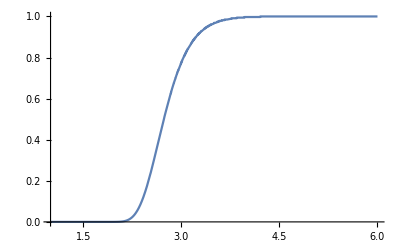

```mathematica
Plot[(1-(T^2 λ^2)/(4π)ⅇ^(-T^2/2)1/((a^2+T^2)^(3/2))(√(a^2+T^2)-√(π/2)T^2 ⅇ^(T^4/(2(a^2+T^2)))Erfc[T^2/(√(2(a^2+T^2)))]))^(10^14/T),{T,1,6}]
```

However, for some reason NSolve doesn’t seem to be able to find a solution.

```mathematica
NSolve[(1-(T^2 λ^2)/(4π)ⅇ^(-T^2/2)1/((a^2+T^2)^(3/2))(√(a^2+T^2)-√(π/2)T^2 ⅇ^(T^4/(2(a^2+T^2)))Erfc[T^2/(√(2(a^2+T^2)))]))^(10^14/T)==0.1,T]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{}

We can however, graphically guess an approximate solution T=2.4 Ω^-1=2.4 x10^-14 s

```mathematica
(1-(T^2 λ^2)/(4π)ⅇ^(-T^2/2)1/((a^2+T^2)^(3/2))(√(a^2+T^2)-√(π/2)T^2 ⅇ^(T^4/(2(a^2+T^2)))Erfc[T^2/(√(2(a^2+T^2)))]))^(10^14/T)/.T-> 2.4
```

0.104134

### c)

We now repeat the computations of a) with the time scales now between T=10^-6 s=10^3 Ω^-1 to T=1s=10^9 Ω^-1 and the new coupling constant

```mathematica
λ=0.1;
```

```mathematica
TableForm[Table[{T,N[(T^2 λ^2)/(4π)ⅇ^(-T^2/2)1/((a^2+T^2)^(3/2))(√(a^2+T^2)-√(π/2)T^2 ⅇ^(T^4/(2(a^2+T^2)))Erfc[T^2/(√(2(a^2+T^2)))])],λ^2/π^2 NIntegrate[u/(1+u)^2 ⅇ^(-1/2 a^2 u^2)Sin[((1+u)T)/2]^2,{u,0,∞}]},{T,Table[10^n,{n,3,9}]}],TableHeadings->{None,{"T(Ω^-1)","P_(g →  e,  Gaussian)","P_(g →  e,  Sudden)"}}]
```

General::munfl: Exp[-500000.] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 4.13418 and 0.0110107 for the integral and error estimates.

General::munfl: Exp[-5.×10^7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 4.13418 and 0.0110137 for the integral and error estimates.

General::munfl: Exp[-5.×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {4.81037×10^7}. NIntegrate obtained 4.13421 and 0.0109755 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

T(Ω^-1) | P_(g →  e,  Gaussian) | P_(g →  e,  Sudden)
1000 | 0. | 0.0041888
10000 | 0. | 0.0041888
100000 | 0. | 0.00418883
1000000 | 0. | 0.00418866
10000000 | 0. | 0.00290664
100000000 | 0. | 0.00265697
1000000000 | 0. | 0.00265448

#### d)

Repeating the same technique as before, we have

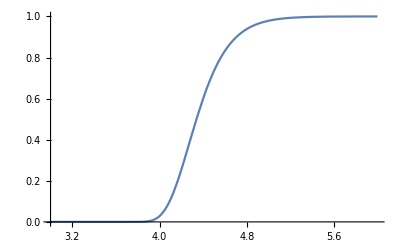

```mathematica
Plot[(1-(T^2 λ^2)/(4π)ⅇ^(-T^2/2)1/((a^2+T^2)^(3/2))(√(a^2+T^2)-√(π/2)T^2 ⅇ^(T^4/(2(a^2+T^2)))Erfc[T^2/(√(2(a^2+T^2)))]))^(10^9/T),{T,3,6}]
```

We thus guess T=4.1 Ω^-1=4.1 x10^-9 s.

```mathematica
(1-(T^2 λ^2)/(4π)ⅇ^(-T^2/2)1/((a^2+T^2)^(3/2))(√(a^2+T^2)-√(π/2)T^2 ⅇ^(T^4/(2(a^2+T^2)))Erfc[T^2/(√(2(a^2+T^2)))]))^(10^9/T)/.T-> 4.1
```

0.108461